Set Environment

```mathematica
root = NotebookDirectory[];
path = Select[
Select[FileNames["*",root,Infinity],DirectoryQ],
!StringMatchQ[#,RegularExpression["(.*\\.git.*)"]]&];
Map[(AppendTo[$Path, #1])&,path];
```

Coding: Graph

## Working:

```mathematica
img = Import["1.png"];
```

```mathematica
TextRecognize[img]
```

Recent developments in dentin bonding

BERND HALLER, DR Mtn Daw

ABSTRACT: Hybridization ofthe dentin with resin by monomer interdiffusion has been identified as thc basic bonding
mechanism resulting in an intimate interlocking ofthe cured resin with the dentin. Today, growing efforts are made to
simplify and shorten the bonding procedures, eg. by combining the functions of primer and adhesive. Ultrastructural
investigations using high-resolution optical technology provided exciting insight into the interactions of bonding sys-
tems and dentin. It became clear` that the maintenance or recovery ofmicroporosities in the dentin is most important for
optimal hybridization. This can be achieved by the moist bonding technique, which is mandatory in acetone-based sys-
tems. The observation that certain bonding systems are able to bond to dentin depleted front the demineralized collagen
network raised the question of whether the collagen-resin interdiffusion zone really represents a prerequisite for suc-
cessful bonding to dentin. The use ofstrongly acidic primer monomers introduced the concept of"self-etching" printers
not only to dentin but also to enamel, which elintinates the necessity ofa separate conditioning step. Clintcal investiga-
tions are necessary to evaluate the potential of recently developed all-in-one products which combine the functions of
conditioner, primer, and adhesive. With improvements in dentin bonding and the development of new resins that ex-
hibit little or no shrinkage upon polymerization, even greater applications for adhesive technology will be found in
dentistry. (Am J Dem 2000;13:44-50).

CLINICAL stGNtFtCANCE: Selection ot" materials and techniques in adhesive dentistry must be orientated to optimal hy-
bridization of the dentin. When total-etching is used, :t moist bonding protocol should be followed, particularly in the
case of acetone-based systems. Self-conditioning enamel and dentin primers offer an interesting altemative since they
avoid the exposure ofunprotected collagen fibers. All-in-one condiprittter-adhesives ntust prove their ability to create a

durable bond to both enamel and dentin before they can be recommended for routine use. -

CORRESPONDENCE: Prof. Bernd Haller, Dept. of Conservative Dentistry, Pcriodontology and Pediatric Dentistry, Uni-

versity Hospital Ulnt. Albert-Einstein-Allee ll,
bemd.haller@medizin.uni-ulm.de

Introduction

The efficacy of dentin bonding systems (DBS) has been
substantially improved in the past 10 yrs. ln modern restora-
tive dentistry, DBS are employed to increase the retention of
resin-based composite (RBC) restorations, which is mainly
important in Class V and IV, and to improve the marginal
adaptation at gingival margins located in dentin. DBS are also
used to seal the dentin and maintain the internal adaptation of
the RBC in order to prevent or treat dentin hypersensitivity.
ln addition. they contribute to the stabilization of both the
prepared tooth and the restoration.

This article focuses on some aspects of DBS and RBC
which are being controversially discussed at the moment,
such as the current status of one-bottle or two-step DBS, the
rationale and necessity of moist or wet bonding, the role of
the collagen-resin hybrid layer, and the potential of self-con-
ditioning primers and primer-adhesives (Table).

Mechanisms of dentin bonding

One major reason why successful bonding to dentin was
so difficult to achieve is that dentin is an intrinsically wet
substrate. The bonding area is connected with the pulp by
dentin tubules which are filled with dentin fluid, a serum-like
tissue fluid derived from the pulp. Another obstacle to an in-
timate contact between resin and dentin is the so-eallcd smear
layer consisting of damaged collagen and apatite which cov-
ers the dentin after cavity preparation and caries excavation.
ln the early days of dentin bonding, the removal of the smear

D-8908I

Ulm, Germany. Fax: 49 731 5023673. E-mail:

layer by acid etching had been discussed as an option for cre-
ating micro-mechanical retention. However, the removal of
the smear plugs from the dentin tubules increases the out-
ward-flow of dentin fluid and the wetness of the dentin sur-
face."3 Without an adequate post-etching treatment of the
dentin, this resulted in dramatic failures including severe
postoperative sensitivity and pulpal irritation.

lvlajor advances have been achieved by the introduction of
primers which promote wetting ofthe dentin with the bonding
agent, and penetration of the bonding agent into the dentin.
Primer monomers are amphiphilic, Le. they contain hydro-
philic groups (eg. -Ol-l, -COOH) for better compatibility of
the resin monomers with the moist dentin, and hydrophobic
methaerylate groups for the co-polymerization with the
bonding resin. Nakabayashi 8a Pashley’ have summarized the
function of dentin primers to be " o maintain or recover the
porosity ofthe demineralized dentin"

In the majority of current DBS. the smear layer is dis-
solved by inorganic acids (eg. phosphoric acid), organic ae-
ids (eg. maleic acid) or acidic monomers (eg. phenyl-P).
Traditional dentin bonding protocols include (I) etch-
ing/conditioning, (2) application ofa primer` and (3) applica-
tion ofa bonding resin or adhesive. lt is, however, not neces-
sary that these steps (l-3) are performed sequentially. Some
of the functions (Le. conditioning, priming, bonding) have
been combined in the form of self-conditioning primers (eg.
A.R.T. Bond.a syntac Questo) and primer-adhesives tag.
OptiBond Solo,g Prime ti' Bond NTIi Syntac Sprinl°), respec-

```mathematica
g10 = genGraph[10,15];
```

```mathematica
AdjacencyMatrix[g10]//MatrixForm
```

AdjacencyMatrix::graph: A graph object is expected at position 1 in AdjacencyMatrix[genGraph[10,15]].

AdjacencyMatrix[genGraph[10,15]]

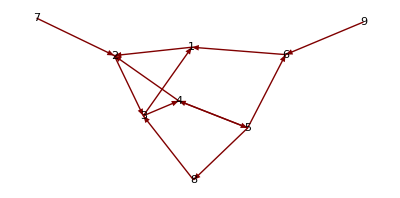

```mathematica
GraphPlot[g10,VertexLabeling->True]
```

```mathematica
g10
```

-Graphics-

## Functions

```mathematica
genGraph[vn_,en_]:=Graph[MapThread[Rule,{RandomInteger[{1,vn},en],RandomInteger[{1,vn},en]}]];
genOrderAdjMatrix[list_]:=SparseArray[Outer[If[#1≤#2,1,0]&,list,list]];
showGraph[list_]:=Block[{g,i},
g=AdjacencyGraph[genOrderAdjMatrix[list]-IdentityMatrix[Length[list],SparseArray]];
Graph[g, VertexLabels-> Table[i->list[[i]],{i,Length[list]}]]];
```

```mathematica
joinOrderAdjMatrix[li1_,li2_]:=SparseArray[Outer[If[#1≤#2,1,0]&,Join[li1,li2],Join[li1,li2]]];
```

## Testing

```mathematica
l1 = Sort[{2,5,1,9,3}]; l2=Sort[{43,56,2,4,1,19,9,12}];
```

```mathematica
a1=genOrderAdjMatrix[l1];a2=genOrderAdjMatrix[l2];
```

```mathematica
{l1,l2}
```

{{1,2,3,5,9},{1,2,4,9,12,19,43,56}}

```mathematica
MatrixForm/@{a1,a2}
```

{(1 | 1 | 1 | 1 | 1
0 | 1 | 1 | 1 | 1
0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 1),(1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 0 | 1 | 1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)}

```mathematica
A=joinOrderAdjMatrix[l1,l2];MatrixForm@A
```

(1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 0 | 1 | 1 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
A . SparseArray[Table[1,13]]//MatrixForm
```

(13
11
9
7
6
13
11
8
6
4
3
2
1)

(1
1
1
0
1)

```mathematica
MatrixForm@a
```

(1 | 1 | 0 | 1 | 1
0 | 1 | 0 | 1 | 0
1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 1 | 0
0 | 1 | 0 | 1 | 1)

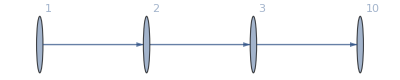

```mathematica
g=Graph[{1-> 2, 2-> 3, 3-> 10}, VertexLabels-> "Name"]
```

```mathematica
A=AdjacencyMatrix[g]
```

SparseArray[…]

```mathematica
MatrixForm@A
```

(0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1
0 | 0 | 0 | 0)

```mathematica
Matrix
```

```mathematica
A .{0,1,0,0}
```

{1,0,0,0}

```mathematica
Timing[g100k = genGraph[100000,500000];]
```

{0.703125,Null}

```mathematica
Timing[g1M = genGraph[1000000,9000000];]
```

{15.2656,Null}

```mathematica
Plot3D[{x Log[y],y Log[x],x+y},{x,10,1000},{y,10,1000}]
```

-Graphics3D-

```mathematica
Text
```